```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

```mathematica
steps = Flatten@Import["step_file.txt","Table"];
taus = Flatten@Import["tau_file.txt","Table"];
```

```mathematica
points = Table[{taus[[i]],steps[[i]]},{i,Length@taus}];
```

```mathematica
tau0 = 1/Pi(1/121 + 1/121)^(1/2)//N
```

0.0409235

```mathematica
K0 =  1/Pi(1/121 + 1/121)^(-1/2)Log[1/10^-4]//N
```

22.8036

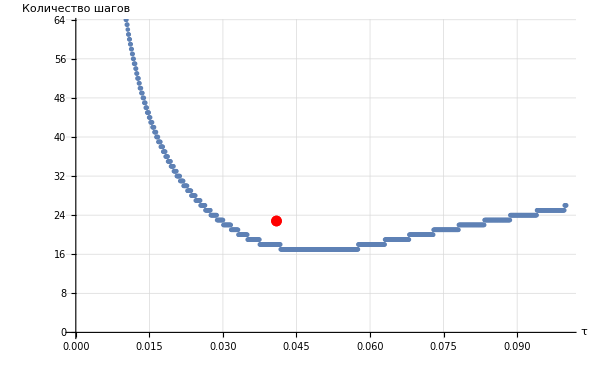

```mathematica
Show[ListPlot[points, ImageSize->600,AxesLabel->{"τ","Количество шагов"},GridLines->Automatic],ListPlot[{{tau0,K0}},PlotStyle->Red]]
```